```mathematica
Hq=DiracDelta[x-β-ξ*α]*(Gamma[2*b0+2]*((1-Abs[β])^2-α^2)^b0/(2^(2*b0+1)*(Gamma[b0+1])^2*(1-Abs[β])^(2b0+1)))*Nv*β^(a-1)*(1-β)^b1*(1+c*β^d)/(1-t/λ^2);
Ha=Assuming[β>-1&&β<1&&x∈Reals&&ξ∈Reals,Integrate[Hq,{α,Abs[β]-1,Abs[β]+1}]];
Hax=Ha/.{a->0.7,b1->2.03,c->13.8,d->2,Nv->1/2,b0->2,ξ->0.3,λ->0.79,t->-1};
```

```mathematica
ReHa=Integrate[Hax,{β,-1,1}];
```

```mathematica
Plot[Re[ReHa],{x,-0.3,0.3}]
```

-Graphics-

```mathematica
ReHa/.{x->0}
```

Undefined

```mathematica
Information[Undefined]
```

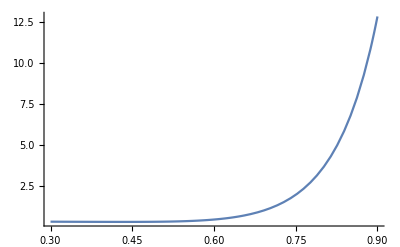

```mathematica
Plot[Re[ReHa],{x,0.3,0.9},PlotRange->All]
```